```mathematica
(*Method defined by D.F. Andrews, "Plots of High Dimensional Data"*)
```

```mathematica
hdSimp[x_]:= Module[{dataLength,tempData, plotData},
finFun = x[[1]]/Sqrt[2];
tempData =  x[[2;;-1]];
If[Mod[Length[tempData],2]==1,AppendTo[tempData,0]];
plotData = Flatten[Table[{Sin[i*t],Cos[i*t]},{i,1, Round[Length[tempData]/2]}]];
x[[1]]/Sqrt[2] + Total[MapThread[#1*#2 &,{tempData,plotData}]]
]
```

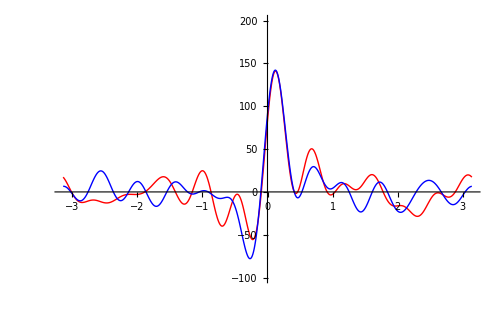

```mathematica
(*Generate random data*)
foo = Table[i,{i,2,14}];
deck = Flatten[AppendTo[foo,{foo,foo,foo}]];
mixdeck = RandomSample[deck, 52];
p1 = mixdeck[[1;;26]];
p2 = mixdeck[[27;;-1]];
Plot[{hdSimp[p1],hdSimp[p2]},{t, -Pi,Pi}, ImageSize->500,PlotStyle->{Red,Blue}, PlotRange->{{-Pi,Pi},{-100,200}}]
```

```mathematica
p1
p2
```

{6,5,14,13,7,13,2,8,14,13,4,6,6,5,8,5,9,8,2,12,3,14,3,10,7,7}

{5,3,8,12,9,12,6,13,4,11,11,10,7,9,11,14,10,12,4,3,11,9,2,10,4,2}